# Exact equations

## Definition

An exact differential equation is an equation of the form dy/dx=f(x,y), where the function f can be expressed as two functions -(M(x,y))/(N(x,y))

We can rewrite this as dy/dx=-(M(x,y))/(N(x,y)), which is M(x,y)dx+N(x,y)dy=0

What then makes our differential equation an exact equation is when we have (∂M)/(∂y)=(∂N)/(∂x), M(x,y)=(∂f)/(∂x) and N(x,y)=(∂f)/(∂y)

### Example problem

```mathematica
Hyperlink["https://www.youtube.com/watch?v=jjtikhR5Zro&index=18&list=PLsu0TcgLDUiJF5u8tbcnyxjAFhqiSyGnJ"]
```

Solve dy/dx=(-2xy)/(x^2-1)

2xydx=-(x^2-1)dy
2xydx+(x^2-1)dy=0
M(x,y)=2xy
N(x,y)=x^2-1
(∂M)/(∂y)=2x,(∂N)/(∂x)=2x
(∂f)/(∂x)=2xy
∂f=2xy∂x
∫∂f=2y∫xⅆx
f(x,y)=x^2 y+g(y)
(∂f)/(∂y)=x^2+dg/dy=N(x,y)=x^2-1
dg/dy=-1
dg=-dy
g(y)=-y+c
f(x,y)=x^2 y-y+c
x^2 y-y=c
y=c/(x^2-1)

Note that this problem could also have been solved using separation of variables

```mathematica
sol=DSolve[y'[x]==(-2*x*y[x])/(x^2-1),y[x],x]
```

{{y[x]→C[1]/(-1+x^2)}}

We can plot solutions based on the constant c

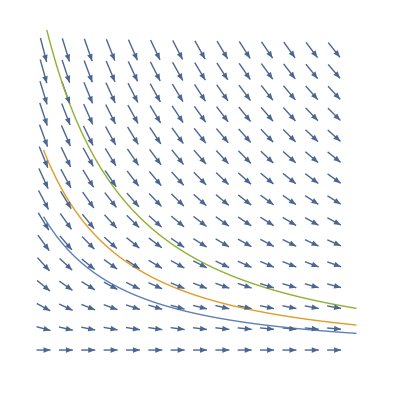

```mathematica
Show[VectorPlot[{1,(-2*x*y)/(x^2-1)},{x,2,5},{y,0,1.5},VectorScale->{0.04,0.04,None}],Plot[{y[x]/.sol/.C[1]->2,y[x]/.sol/.C[1]-> 3,y[x]/.sol/.C[1]->5},{x,2,5},PlotStyle->Thick],Frame->None,Axes->False]
```

### Example problem

```mathematica
Hyperlink["https://www.youtube.com/watch?v=CyijD6AVh2Q&list=PLsu0TcgLDUiJF5u8tbcnyxjAFhqiSyGnJ&index=19"]
```

Solve (ⅇ^(2y)-ycos(xy))dx+(2xⅇ^(2y)-xcos(xy))dy=0

Taking the partial derivatives (∂M)/(∂y) and (∂N)/(∂x) to show that this is an exact equation

```mathematica
D[ⅇ^(2y)-y*Cos[x*y],y]
```

2 ⅇ^(2 y)-Cos[x y]+x y Sin[x y]

```mathematica
D[2*x*ⅇ^(2*y)-x*Cos[x*y],x]
```

2 ⅇ^(2 y)-Cos[x y]+x y Sin[x y]

```mathematica
DSolve[y'[x]==Simplify[(-(ⅇ^(2y[x])-y[x]*Cos[x*y[x]]))/(2*x*ⅇ^(2*y[x])-x*Cos[x*y[x]])],y[x],x]
```

Solve[ⅇ^(2 y[x]) x-Sin[x y[x]]==C[1],y[x]]

The slope field

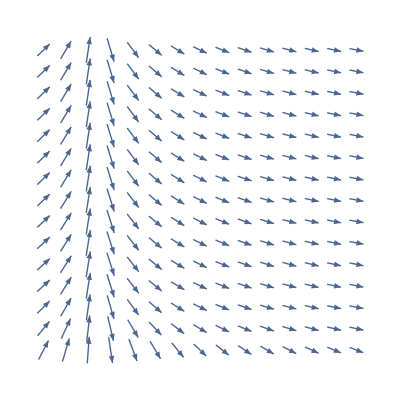

```mathematica
VectorPlot[{1,(-(ⅇ^(2y)-y*Cos[x*y]))/(2*x*ⅇ^(2*y)-x*Cos[x*y])},{x,-1,5},{y,0,3},VectorScale->{0.04,0.04,None},Frame->False]
```

## More YouTube example problems

```mathematica
Hyperlink["https://www.youtube.com/watch?v=HLO2UxJjRB8&index=20&list=PLsu0TcgLDUiJF5u8tbcnyxjAFhqiSyGnJ"]
```

Solve dy/dx=(xy^2-sin(x)cos(x))/(y(1-x^2)), y(0)=2

```mathematica
DSolve[{y'[x]==(x*y[x]^2-Sin[x]*Cos[x])/(y[x]*(1-x^2)),y[0]==2},y[x],x]
```

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

{{y[x]→(√(-3-Cos[x]^2))/(√(-1+x^2))}}

Let’s do this step-by-step

First we will check to see if we have an exact equation

```mathematica
(*Partial derivative of M with respect to y*)
D[x*y^2-Sin[x]*Cos[x],y]
```

2 x y

```mathematica
(*Partial derivative of N with respect to x*)
D[-y*(1-x^2),x]
```

2 x y

```mathematica
(*Are they equal?*)
D[x*y^2-Sin[x]*Cos[x],y]==D[-y*(1-x^2),x]
```

True

```mathematica
(*Calculating the f(x,y), not forgetting the arbitrary h(x) that Mathematic will not add*)
∫(x^2*y-y)ⅆy
```

1/2 (-1+x^2) y^2

```mathematica
(*Calculating h from the fact that M equals the partial derivative of f with respect to x*)
D[1/2 (-1+x^2) y^2,x]
```

x y^2

```mathematica
∫-Cos[x]*Sin[x]ⅆx
```

Cos[x]^2/2

Now we have f(x,y)=1/2 (-1+x^2) y^2+Cos[x]^2/2+c=0

```mathematica
(*From the initial value problem we have that x=0 and y(0)=2*)
Solve[1/2 (-1+0^2) 2^2+Cos[0]^2/2+c==0,c]
```

{{c→3/2}}

The final solution is then 1/2 (-1+x^2) y^2+Cos[x]^2/2=-3/2, which simplifies to the solution at the start

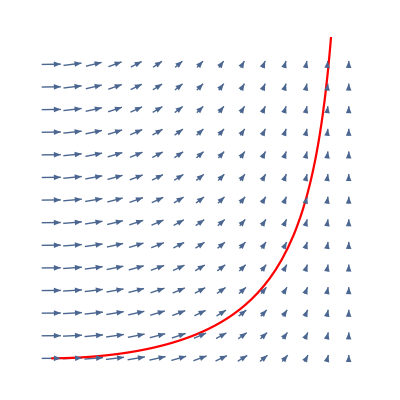

```mathematica
Show[VectorPlot[{1,(x*y^2-Sin[x]*Cos[x])/(y*(1-x^2))},{x,0.01,0.99},{y,2,5},VectorScale->{0.02,0.02,None},Frame->False],Plot[Sqrt[(3+Cos[x]^2)/(1-x^2)],{x,0.01,0.99},PlotStyle->Red]]
```

```mathematica
Hyperlink["https://www.youtube.com/watch?v=BE65YyTVZnM&index=22&list=PLsu0TcgLDUiJF5u8tbcnyxjAFhqiSyGnJ"]
```

Solve dy/dx=xy/(20-2 x^2-3 y^2)

```mathematica
DSolve[y'[x]==(x*y[x])/(20-2*x^2-3*y[x]^2),y[x],x]
```

{{y[x]→-√(10/3-x^2/3+100/(3 (1000-300 x^2+30 x^4-x^6+27 C[1]+3 √3 √(2000 C[1]-600 x^2 C[1]+60 x^4 C[1]-2 x^6 C[1]+27 C[1]^2))^(1/3))-(20 x^2)/(3 (1000-300 x^2+30 x^4-x^6+27 C[1]+3 √3 √(2000 C[1]-600 x^2 C[1]+60 x^4 C[1]-2 x^6 C[1]+27 C[1]^2))^(1/3))+x^4/(3 (1000-300 x^2+30 x^4-x^6+27 C[1]+3 √3 √(2000 C[1]-600 x^2 C[1]+60 x^4 C[1]-2 x^6 C[1]+27 C[1]^2))^(1/3))+1/3 (1000-300 x^2+30 x^4-x^6+27 C[1]+3 √3 √(2000 C[1]-600 x^2 C[1]+60 x^4 C[1]-2 x^6 C[1]+27 C[1]^2))^(1/3))},{y[x]→√(10/3-x^2/3+100/(3 (1000-300 x^2+30 x^4-x^6+27 C[1]+3 √3 √(2000 C[1]-600 x^2 C[1]+60 x^4 C[1]-2 x^6 C[1]+27 C[1]^2))^(1/3))-(20 x^2)/(3 (1000-300 x^2+30 x^4-x^6+27 C[1]+3 √3 √(2000 C[1]-600 x^2 C[1]+60 x^4 C[1]-2 x^6 C[1]+27 C[1]^2))^(1/3))+x^4/(3 (1000-300 x^2+30 x^4-x^6+27 C[1]+3 √3 √(2000 C[1]-600 x^2 C[1]+60 x^4 C[1]-2 x^6 C[1]+27 C[1]^2))^(1/3))+1/3 (1000-300 x^2+30 x^4-x^6+27 C[1]+3 √3 √(2000 C[1]-600 x^2 C[1]+60 x^4 C[1]-2 x^6 C[1]+27 C[1]^2))^(1/3))},{y[x]→-√(10/3-x^2/3-50/(3 (1000-300 x^2+30 x^4-x^6+27 C[1]+3 √3 √(2000 C[1]-600 x^2 C[1]+60 x^4 C[1]-2 x^6 C[1]+27 C[1]^2))^(1/3))+(50 ⅈ)/(√3 (1000-300 x^2+30 x^4-x^6+27 C[1]+3 √3 √(2000 C[1]-600 x^2 C[1]+60 x^4 C[1]-2 x^6 C[1]+27 C[1]^2))^(1/3))+(10 x^2)/(3 (1000-300 x^2+30 x^4-x^6+27 C[1]+3 √3 √(2000 C[1]-600 x^2 C[1]+60 x^4 C[1]-2 x^6 C[1]+27 C[1]^2))^(1/3))-(10 ⅈ x^2)/(√3 (1000-300 x^2+30 x^4-x^6+27 C[1]+3 √3 √(2000 C[1]-600 x^2 C[1]+60 x^4 C[1]-2 x^6 C[1]+27 C[1]^2))^(1/3))-x^4/(6 (1000-300 x^2+30 x^4-x^6+27 C[1]+3 √3 √(2000 C[1]-600 x^2 C[1]+60 x^4 C[1]-2 x^6 C[1]+27 C[1]^2))^(1/3))+(ⅈ x^4)/(2 √3 (1000-300 x^2+30 x^4-x^6+27 C[1]+3 √3 √(2000 C[1]-600 x^2 C[1]+60 x^4 C[1]-2 x^6 C[1]+27 C[1]^2))^(1/3))-1/6 (1000-300 x^2+30 x^4-x^6+27 C[1]+3 √3 √(2000 C[1]-600 x^2 C[1]+60 x^4 C[1]-2 x^6 C[1]+27 C[1]^2))^(1/3)-(ⅈ (1000-300 x^2+30 x^4-x^6+27 C[1]+3 √3 √(2000 C[1]-600 x^2 C[1]+60 x^4 C[1]-2 x^6 C[1]+27 C[1]^2))^(1/3))/(2 √3))},{y[x]→√(10/3-x^2/3-50/(3 (1000-300 x^2+30 x^4-x^6+27 C[1]+3 √3 √(2000 C[1]-600 x^2 C[1]+60 x^4 C[1]-2 x^6 C[1]+27 C[1]^2))^(1/3))+(50 ⅈ)/(√3 (1000-300 x^2+30 x^4-x^6+27 C[1]+3 √3 √(2000 C[1]-600 x^2 C[1]+60 x^4 C[1]-2 x^6 C[1]+27 C[1]^2))^(1/3))+(10 x^2)/(3 (1000-300 x^2+30 x^4-x^6+27 C[1]+3 √3 √(2000 C[1]-600 x^2 C[1]+60 x^4 C[1]-2 x^6 C[1]+27 C[1]^2))^(1/3))-(10 ⅈ x^2)/(√3 (1000-300 x^2+30 x^4-x^6+27 C[1]+3 √3 √(2000 C[1]-600 x^2 C[1]+60 x^4 C[1]-2 x^6 C[1]+27 C[1]^2))^(1/3))-x^4/(6 (1000-300 x^2+30 x^4-x^6+27 C[1]+3 √3 √(2000 C[1]-600 x^2 C[1]+60 x^4 C[1]-2 x^6 C[1]+27 C[1]^2))^(1/3))+(ⅈ x^4)/(2 √3 (1000-300 x^2+30 x^4-x^6+27 C[1]+3 √3 √(2000 C[1]-600 x^2 C[1]+60 x^4 C[1]-2 x^6 C[1]+27 C[1]^2))^(1/3))-1/6 (1000-300 x^2+30 x^4-x^6+27 C[1]+3 √3 √(2000 C[1]-600 x^2 C[1]+60 x^4 C[1]-2 x^6 C[1]+27 C[1]^2))^(1/3)-(ⅈ (1000-300 x^2+30 x^4-x^6+27 C[1]+3 √3 √(2000 C[1]-600 x^2 C[1]+60 x^4 C[1]-2 x^6 C[1]+27 C[1]^2))^(1/3))/(2 √3))},{y[x]→-√(10/3-x^2/3-50/(3 (1000-300 x^2+30 x^4-x^6+27 C[1]+3 √3 √(2000 C[1]-600 x^2 C[1]+60 x^4 C[1]-2 x^6 C[1]+27 C[1]^2))^(1/3))-(50 ⅈ)/(√3 (1000-300 x^2+30 x^4-x^6+27 C[1]+3 √3 √(2000 C[1]-600 x^2 C[1]+60 x^4 C[1]-2 x^6 C[1]+27 C[1]^2))^(1/3))+(10 x^2)/(3 (1000-300 x^2+30 x^4-x^6+27 C[1]+3 √3 √(2000 C[1]-600 x^2 C[1]+60 x^4 C[1]-2 x^6 C[1]+27 C[1]^2))^(1/3))+(10 ⅈ x^2)/(√3 (1000-300 x^2+30 x^4-x^6+27 C[1]+3 √3 √(2000 C[1]-600 x^2 C[1]+60 x^4 C[1]-2 x^6 C[1]+27 C[1]^2))^(1/3))-x^4/(6 (1000-300 x^2+30 x^4-x^6+27 C[1]+3 √3 √(2000 C[1]-600 x^2 C[1]+60 x^4 C[1]-2 x^6 C[1]+27 C[1]^2))^(1/3))-(ⅈ x^4)/(2 √3 (1000-300 x^2+30 x^4-x^6+27 C[1]+3 √3 √(2000 C[1]-600 x^2 C[1]+60 x^4 C[1]-2 x^6 C[1]+27 C[1]^2))^(1/3))-1/6 (1000-300 x^2+30 x^4-x^6+27 C[1]+3 √3 √(2000 C[1]-600 x^2 C[1]+60 x^4 C[1]-2 x^6 C[1]+27 C[1]^2))^(1/3)+(ⅈ (1000-300 x^2+30 x^4-x^6+27 C[1]+3 √3 √(2000 C[1]-600 x^2 C[1]+60 x^4 C[1]-2 x^6 C[1]+27 C[1]^2))^(1/3))/(2 √3))},{y[x]→√(10/3-x^2/3-50/(3 (1000-300 x^2+30 x^4-x^6+27 C[1]+3 √3 √(2000 C[1]-600 x^2 C[1]+60 x^4 C[1]-2 x^6 C[1]+27 C[1]^2))^(1/3))-(50 ⅈ)/(√3 (1000-300 x^2+30 x^4-x^6+27 C[1]+3 √3 √(2000 C[1]-600 x^2 C[1]+60 x^4 C[1]-2 x^6 C[1]+27 C[1]^2))^(1/3))+(10 x^2)/(3 (1000-300 x^2+30 x^4-x^6+27 C[1]+3 √3 √(2000 C[1]-600 x^2 C[1]+60 x^4 C[1]-2 x^6 C[1]+27 C[1]^2))^(1/3))+(10 ⅈ x^2)/(√3 (1000-300 x^2+30 x^4-x^6+27 C[1]+3 √3 √(2000 C[1]-600 x^2 C[1]+60 x^4 C[1]-2 x^6 C[1]+27 C[1]^2))^(1/3))-x^4/(6 (1000-300 x^2+30 x^4-x^6+27 C[1]+3 √3 √(2000 C[1]-600 x^2 C[1]+60 x^4 C[1]-2 x^6 C[1]+27 C[1]^2))^(1/3))-(ⅈ x^4)/(2 √3 (1000-300 x^2+30 x^4-x^6+27 C[1]+3 √3 √(2000 C[1]-600 x^2 C[1]+60 x^4 C[1]-2 x^6 C[1]+27 C[1]^2))^(1/3))-1/6 (1000-300 x^2+30 x^4-x^6+27 C[1]+3 √3 √(2000 C[1]-600 x^2 C[1]+60 x^4 C[1]-2 x^6 C[1]+27 C[1]^2))^(1/3)+(ⅈ (1000-300 x^2+30 x^4-x^6+27 C[1]+3 √3 √(2000 C[1]-600 x^2 C[1]+60 x^4 C[1]-2 x^6 C[1]+27 C[1]^2))^(1/3))/(2 √3))}}

This looks terrible, so let’s do it step by step

We are going to use an integrating factor

```mathematica
D[x*y,y]
```

x

```mathematica
D[3*y^2+2*x^2-20,x]
```

4 x

```mathematica
ⅇ^(∫(D[x*y,y]-D[3*y^2+2*x^2-20,x])/(3*y^2+2*x^2-20)ⅆx)
```

1/((-20+2 x^2+3 y^2)^(3/4))

This is unfortunately not a single variable function

```mathematica
ⅇ^(∫(D[3*y^2+2*x^2-20,x]-D[x*y,y])/(x*y)ⅆy)
```

y^3

This is a single variable function and becomes our integrating factor

```mathematica
(*Checking to see if we now have an exact equation*)
D[y^3*x*y,y]
D[y^3*(3*y^2+2*x^2-20),x]
```

4 x y^3

4 x y^3

```mathematica
(*We now use the fact that μM is the partial derivative of f with respect to x*)
(*Don't forget the arbitary g(y) that Mathematica won't add*)
∫y^3*x*yⅆx
```

(x^2 y^4)/2

```mathematica
(*The above result with the g(y) is differentiated with respect to y, which must equal μN*)
(*We integrate to get g(y)*)
∫(3*y^5-20*y^3)ⅆy
```

-5 y^4+y^6/2

The final solution is then f(x,y)=1/2 x^2 y^4+1/2 y^6-5 y^4+c=0